```mathematica
cycles = 2;
sinedata = Table[Sin[x],{x,0,(cycles*2)*Pi,0.001}];
cosinedata = Table[Cos[x],{x,0,(cycles*2)*Pi,0.001}];
```

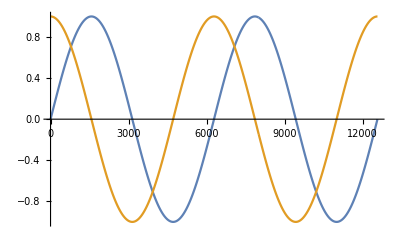

```mathematica
ListLinePlot[{sinedata,cosinedata}]
```

```mathematica
Length[sinedata]
Length[cosinedata]
```

12567

12567

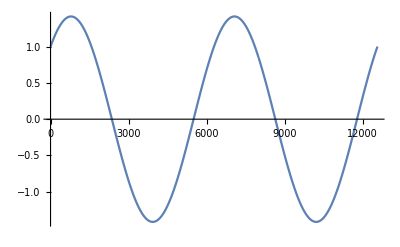

```mathematica
plusdata = sinedata + cosinedata;
ListLinePlot[plusdata]
```

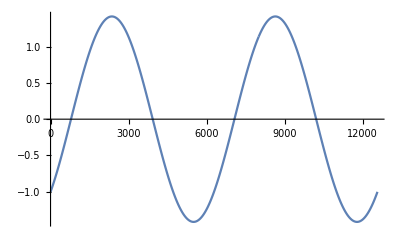

```mathematica
minusdata = sinedata - cosinedata;
ListLinePlot[minusdata]
```

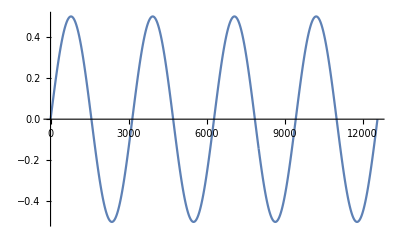

```mathematica
timesdata = sinedata * cosinedata;
ListLinePlot[timesdata]
```

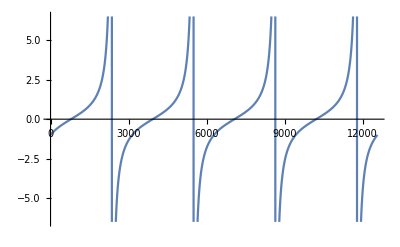

```mathematica
combodata = minusdata / plusdata;
ListLinePlot[combodata]
```

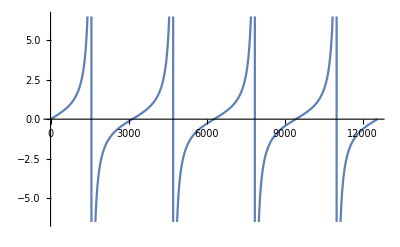

```mathematica
tandata = Table[Tan[x],{x,0,(cycles*2)*Pi,0.001}];
ListLinePlot[tandata]
```

### So (sine - cosine) / (sine + cosine) = tangent?

```mathematica
testandata = Table[(Sin[x]-Cos[x])/ (Sin[x]+Cos[x]),{x,0,(cycles*2)*Pi,0.001}];
ListLinePlot[testandata]
```

-Graphics-

```mathematica
Yes!
```

```mathematica
Sine = o/h 
Cosine = a/h
(o/h - a/h) / (o/h + a/h)
```

```mathematica
Simplify[(o/h - a/h) / (o/h + a/h)]
```

(-a+o)/(a+o)